## reproduction

```mathematica
gra=Item[#,Background->Lighter[Gray, 0.2]]&;
Grid[({{"xNW", "xN", "xNE"}, {"xW", "x", "xE"}, {"xSW", "xS", "xSE"}})/.{"xW"->gra["xW"],"xSW"->gra["xSW"],"xNW"->gra["xNW"]},Frame->All]
```

xNW | xN | xNE
xW | x | xE
xSW | xS | xSE

```mathematica
gra=Item[#,Background->Lighter[Gray, 0.2]]&;
Grid[({{"x'NW", "x'N", "x'NE"}, {"x'W", "x'", "x'E"}, {"x'SW", "x'S", "x'SE"}})/.{"x'"->gra["x'"],"xP_32"->gra["xP_32"],"xP_22"->gra["xP_22"]},Frame->All]
```

x'NW | x'N | x'NE
x'W | x' | x'E
x'SW | x'S | x'SE

```mathematica
lifeVars[]
```

{x,xP,xNW,xN,xNE,xW,xE,xSW,xS,xSE}

```mathematica
lr
```

sat::shdw: Symbol sat appears in multiple contexts {life`,Global`}; definitions in context life` may shadow or be shadowed by other definitions.

plt::shdw: Symbol plt appears in multiple contexts {life`,Global`}; definitions in context life` may shadow or be shadowed by other definitions.

```mathematica
the190ForCellIJ[2,3]
```

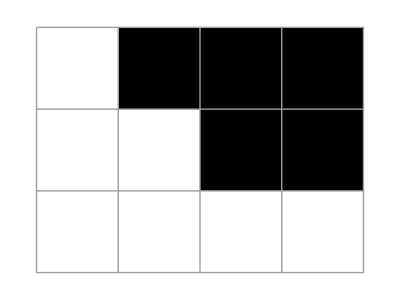
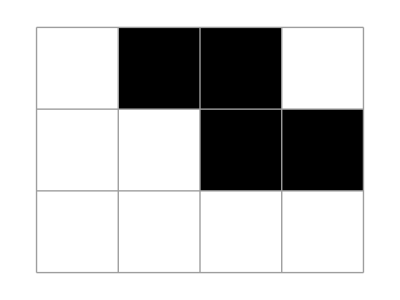
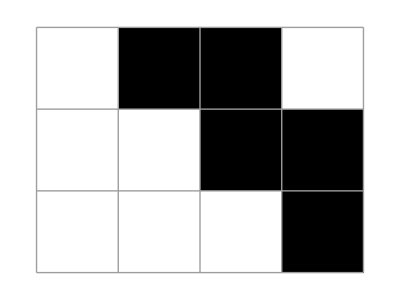
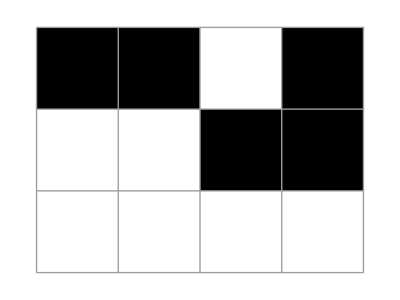
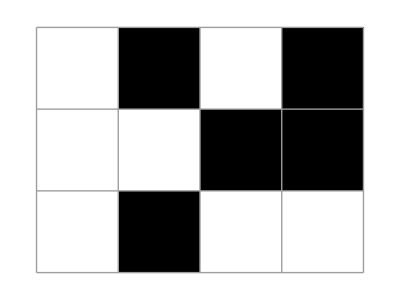
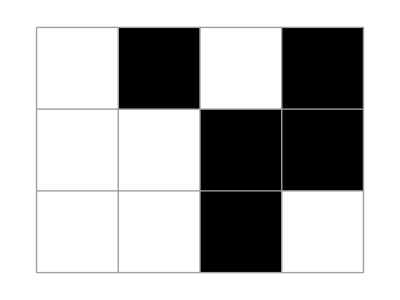
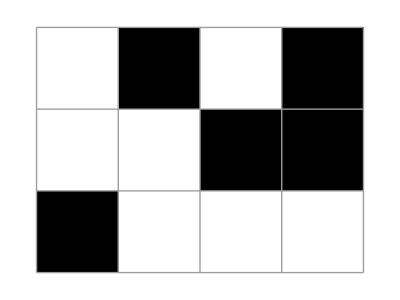
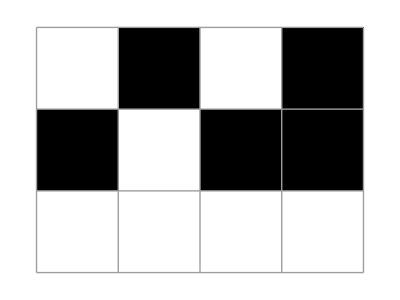
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
lr;
Clear[x22,xP22,xNW22,xN22,xNE22,xW22,xE22,xSW22,xS22,xSE22];
Clear[x23,xP23,xNW23,xN23,xNE23,xW23,xE23,xSW23,xS23,xSE23];
Clear[formula,varList,endStateRules];

endStateRules={
xP22->True
,xP23->True
,x22->False
,x23->False

};
formula=and@{the190ForCellIJ[2,2],the190ForCellIJ[2,3]}/.endStateRules;

varList=Complement[
join@{
lifeVars[2,2]
,lifeVars[2,3]

}/.endStateRules,
{True,False}
];

out=sat[varList,formula,100];
endGame=(Thread[Rule[varList,out[[#]]]]~Join~Boole[endStateRules])&/@Range[Length[out]];
looker=plt[({{xNW22, xN22, xNE22, xNE23}, {xW22, x22, xE22, xE23}, {xSW22, xS22, xSE22, xSE23}})/.#]&;
looker/@endGame
```

```mathematica
and@{lifeVars[2,2],lifeVars[2,3]}
```

x22&&xP22&&xNW22&&xN22&&xNE22&&xW22&&xE22&&xSW22&&xS22&&xSE22&&x23&&xP23&&xNW23&&xN23&&xNE23&&xW23&&xE23&&xSW23&&xS23&&xSE23